# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"New Mexico","Vermont","Washington","Michigan","Utah","Wisconsin"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01","2022-01-15","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-13

```mathematica
states=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Minnesota,Nebraska,Nevada,New Jersey,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Virginia}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Arizona→{{2021-12-30,191},{2021-12-31,109},{2022-01-01,100},{2022-01-02,291},{2022-01-03,267},{2022-01-04,302},{2022-01-05,255},{2022-01-06,272},{2022-01-07,165},{2022-01-08,172},{2022-01-09,329},{2022-01-10,315},{2022-01-11,298},{2022-01-12,16},{2022-01-13,0}},California→{{2021-12-30,722},{2021-12-31,509},{2022-01-01,58},{2022-01-02,1095},{2022-01-03,1749},{2022-01-04,642},{2022-01-05,79},{2022-01-06,47},{2022-01-07,85},{2022-01-08,6},{2022-01-09,19},{2022-01-10,14},{2022-01-11,15},{2022-01-12,0},{2022-01-13,0}},Colorado→{{2021-12-30,645},{2021-12-31,209},{2022-01-01,77},{2022-01-02,96},{2022-01-03,460},{2022-01-04,212},{2022-01-05,192},{2022-01-06,146},{2022-01-07,7},{2022-01-08,3},{2022-01-09,2},{2022-01-10,2},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Connecticut→{{2021-12-30,344},{2021-12-31,191},{2022-01-01,22},{2022-01-02,144},{2022-01-03,264},{2022-01-04,99},{2022-01-05,41},{2022-01-06,6},{2022-01-07,3},{2022-01-08,0},{2022-01-09,0},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Florida→{{2021-12-30,206},{2021-12-31,8},{2022-01-01,30},{2022-01-02,141},{2022-01-03,55},{2022-01-04,32},{2022-01-05,49},{2022-01-06,3},{2022-01-07,15},{2022-01-08,17},{2022-01-09,15},{2022-01-10,0},{2022-01-11,1},{2022-01-12,0},{2022-01-13,0}},Georgia→{{2021-12-30,107},{2021-12-31,3},{2022-01-01,11},{2022-01-02,47},{2022-01-03,149},{2022-01-04,79},{2022-01-05,1},{2022-01-06,0},{2022-01-07,0},{2022-01-08,0},{2022-01-09,1},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Illinois→{{2021-12-30,110},{2021-12-31,32},{2022-01-01,19},{2022-01-02,44},{2022-01-03,49},{2022-01-04,38},{2022-01-05,16},{2022-01-06,14},{2022-01-07,16},{2022-01-08,16},{2022-01-09,18},{2022-01-10,16},{2022-01-11,10},{2022-01-12,0},{2022-01-13,0}},Indiana→{{2021-12-30,12},{2021-12-31,2},{2022-01-01,0},{2022-01-02,21},{2022-01-03,23},{2022-01-04,46},{2022-01-05,15},{2022-01-06,29},{2022-01-07,19},{2022-01-08,0},{2022-01-09,1},{2022-01-10,25},{2022-01-11,13},{2022-01-12,11},{2022-01-13,0}},Louisiana→{{2021-12-30,175},{2021-12-31,38},{2022-01-01,33},{2022-01-02,190},{2022-01-03,45},{2022-01-04,8},{2022-01-05,8},{2022-01-06,25},{2022-01-07,0},{2022-01-08,0},{2022-01-09,0},{2022-01-10,13},{2022-01-11,0},{2022-01-12,1},{2022-01-13,0}},Maryland→{{2021-12-30,85},{2021-12-31,84},{2022-01-01,77},{2022-01-02,93},{2022-01-03,88},{2022-01-04,67},{2022-01-05,70},{2022-01-06,69},{2022-01-07,50},{2022-01-08,61},{2022-01-09,36},{2022-01-10,52},{2022-01-11,37},{2022-01-12,24},{2022-01-13,25}},Massachusetts→{{2021-12-30,1220},{2021-12-31,168},{2022-01-01,169},{2022-01-02,942},{2022-01-03,1629},{2022-01-04,1181},{2022-01-05,877},{2022-01-06,826},{2022-01-07,132},{2022-01-08,6},{2022-01-09,0},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Minnesota→{{2021-12-30,510},{2021-12-31,34},{2022-01-01,12},{2022-01-02,21},{2022-01-03,54},{2022-01-04,25},{2022-01-05,1},{2022-01-06,0},{2022-01-07,0},{2022-01-08,0},{2022-01-09,2},{2022-01-10,0},{2022-01-11,1},{2022-01-12,0},{2022-01-13,0}},Nebraska→{{2021-12-30,30},{2021-12-31,35},{2022-01-01,37},{2022-01-02,34},{2022-01-03,51},{2022-01-04,58},{2022-01-05,41},{2022-01-06,53},{2022-01-07,52},{2022-01-08,42},{2022-01-09,19},{2022-01-10,69},{2022-01-11,53},{2022-01-12,69},{2022-01-13,34}},Nevada→{{2021-12-30,11},{2021-12-31,25},{2022-01-01,0},{2022-01-02,1},{2022-01-03,26},{2022-01-04,27},{2022-01-05,27},{2022-01-06,16},{2022-01-07,18},{2022-01-08,10},{2022-01-09,12},{2022-01-10,46},{2022-01-11,10},{2022-01-12,0},{2022-01-13,0}},New Jersey→{{2021-12-30,189},{2021-12-31,140},{2022-01-01,4},{2022-01-02,21},{2022-01-03,23},{2022-01-04,42},{2022-01-05,125},{2022-01-06,0},{2022-01-07,1},{2022-01-08,0},{2022-01-09,1},{2022-01-10,1},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},New York→{{2021-12-30,247},{2021-12-31,139},{2022-01-01,45},{2022-01-02,528},{2022-01-03,370},{2022-01-04,220},{2022-01-05,179},{2022-01-06,55},{2022-01-07,26},{2022-01-08,17},{2022-01-09,0},{2022-01-10,4},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},North Carolina→{{2021-12-30,259},{2021-12-31,52},{2022-01-01,49},{2022-01-02,74},{2022-01-03,184},{2022-01-04,205},{2022-01-05,129},{2022-01-06,42},{2022-01-07,57},{2022-01-08,53},{2022-01-09,0},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},North Dakota→{{2021-12-30,79},{2021-12-31,21},{2022-01-01,4},{2022-01-02,42},{2022-01-03,70},{2022-01-04,40},{2022-01-05,102},{2022-01-06,11},{2022-01-07,21},{2022-01-08,0},{2022-01-09,4},{2022-01-10,3},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Ohio→{{2021-12-30,120},{2021-12-31,3},{2022-01-01,1},{2022-01-02,9},{2022-01-03,106},{2022-01-04,113},{2022-01-05,101},{2022-01-06,98},{2022-01-07,48},{2022-01-08,0},{2022-01-09,2},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Oregon→{{2021-12-30,101},{2021-12-31,55},{2022-01-01,21},{2022-01-02,21},{2022-01-03,78},{2022-01-04,230},{2022-01-05,195},{2022-01-06,116},{2022-01-07,132},{2022-01-08,72},{2022-01-09,9},{2022-01-10,0},{2022-01-11,1},{2022-01-12,0},{2022-01-13,0}},Pennsylvania→{{2021-12-30,89},{2021-12-31,54},{2022-01-01,3},{2022-01-02,24},{2022-01-03,3},{2022-01-04,16},{2022-01-05,2},{2022-01-06,23},{2022-01-07,22},{2022-01-08,0},{2022-01-09,1},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},South Carolina→{{2021-12-30,148},{2021-12-31,33},{2022-01-01,3},{2022-01-02,24},{2022-01-03,14},{2022-01-04,2},{2022-01-05,15},{2022-01-06,0},{2022-01-07,2},{2022-01-08,7},{2022-01-09,0},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Tennessee→{{2021-12-30,216},{2021-12-31,50},{2022-01-01,6},{2022-01-02,0},{2022-01-03,43},{2022-01-04,3},{2022-01-05,0},{2022-01-06,0},{2022-01-07,0},{2022-01-08,0},{2022-01-09,0},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}},Texas→{{2021-12-30,162},{2021-12-31,20},{2022-01-01,4},{2022-01-02,29},{2022-01-03,102},{2022-01-04,129},{2022-01-05,81},{2022-01-06,43},{2022-01-07,8},{2022-01-08,0},{2022-01-09,0},{2022-01-10,1},{2022-01-11,1},{2022-01-12,0},{2022-01-13,0}},Virginia→{{2021-12-30,41},{2021-12-31,0},{2022-01-01,0},{2022-01-02,3},{2022-01-03,1},{2022-01-04,1},{2022-01-05,0},{2022-01-06,0},{2022-01-07,0},{2022-01-08,0},{2022-01-09,1},{2022-01-10,0},{2022-01-11,0},{2022-01-12,0},{2022-01-13,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

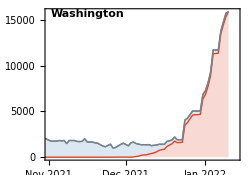

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

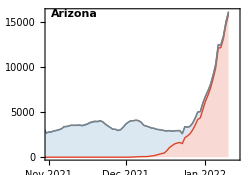
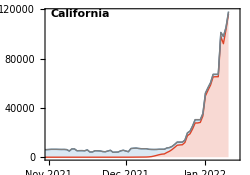
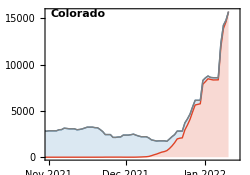
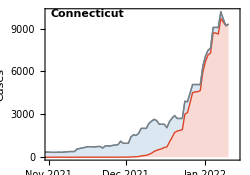
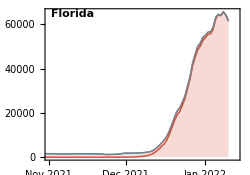
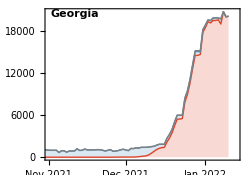
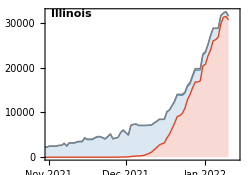
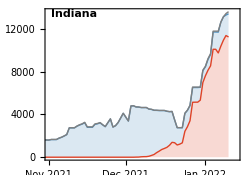
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png